# Testeando ajustes

a...

```mathematica
dataLine={#,#}&/@Range[100];
dataSqrt={#,Sqrt[#]}&/@Range[100];
dataSqare={#,#^2}&/@Range[100];
```

```mathematica
nlm=NonlinearModelFit[dataLine,a x^2+b x+c,{a,b,c},x]
```

FittedModel[-1.13687×10^-14+1. x-4.10566×10^-18 x^2]

```mathematica
nlm["BestFit"]
```

-1.13687×10^-14+1. x-4.10566×10^-18 x^2

```mathematica
nlm["BestFit"]//Chop
```

1. x

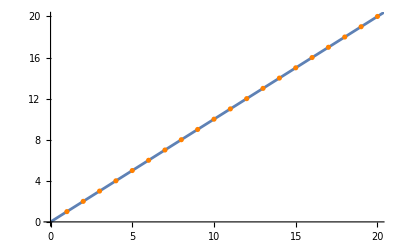

```mathematica
Show[
Plot[nlm[x],{x,0,100}],
ListPlot[dataLine,
PlotStyle->Orange
],
PlotRange->{#,#}&@{0,20}
]
```